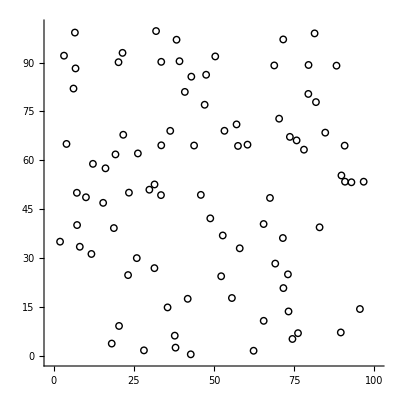
{0.00108,-Graphics-}

```mathematica
(r=1.;list=RandomReal[{0,100},{100,2}];Graphics[Circle[#,r]&/@Complement[list,DeleteDuplicates@Flatten[Delete[#,1]&/@Nearest[list][list,{All,2r}],1]],Axes->True,PlotRange->{{-1.,101.},{-1.,101.}}])//AbsoluteTiming
```